```mathematica
PrependTo[$Path,"/Users/annils14/Documents/KerrModes"];PrependTo[$Path,"~/Research/KerrQNM/KerrModes"];
Needs["KerrTTML`"]
SetSpinWeight[-2]
SelectMode[PolynomialMode]
```

All KerrMode routines (TTML) set for Spin-Weight s = -2

Mode set to find Polynomial solutions

```mathematica
SchTTMLTable[2]=2;
SchTTMLTable[2,0]={0.001-2.001*I,0,0,0,0};
SchTTMLTable[2,1]={0.35-0.27*I,0,0,0,0};
SchTTMLTable[3]=2;
SchTTMLTable[3,0]={0.6-0.09*I,0,0,0,0};
SchTTMLTable[3,1]={0.6-0.28*I,0,0,0,0};
```

```mathematica
SchTTMLTable[2,0]
```

{0.-2. ⅈ,0,0,0,0}

```mathematica
Options[ModeSolution]
```

{JacobianStep→-10,NoNegω→False,QNMPrecision→24,RadialCFDigits→8,RadialCFMinDepth→300,RadialDebug→0,RadialRelax→1,RCFPower→Null[],Rootϵ→Null[],SolutionDebug→0,SolutionIter→50,SolutionOscillate→10,SolutionSlow→10}

```mathematica
SelectMode[PolynomialMode]
```

Mode set to find Polynomial solutions

```mathematica
ModeSolution[0,-2,2,2,1/100,0.0528-1.998ⅈ,4.0,-8,1,300,15,0,0,0,0,SolutionDebug->10,RadialDebug->2]
```

Initial Nradial : 300

ωg = 0.0528-1.998 ⅈ Almg = 4.

ω0 = 0, Alm0 = 0

δω=0.000441649+0.0000436136 ⅈ  root=0.255688

ω=0.0532416-1.99796 ⅈ

δω=-9.385×10^-8+5.64073×10^-7 ⅈ  root=0.000329484

ω=0.0532416-1.99796 ⅈ

δω=1.76501×10^-10+4.40226×10^-11 ⅈ  root=1.04811×10^-7

ω=0.0532416-1.99796 ⅈ

δω=-1.09144×10^-14+3.05856×10^-14 ⅈ  root=1.8711×10^-11

a = 1/100 ω = 0.0532416-1.99796 ⅈ alm = 3.99887+0.053294 ⅈ

Δω = 3.24747×10^-14

Jacobian matrix : {{0.106765,576.173},{-576.173,0.106765}} , rcferr : {300,0.,-0.00213251-0.000036141 ⅈ,{0.963109+0.156908 ⅈ,0.000143571},Null[]}

Nradial : 300 , Nradialnew : 300

δω=-7.3644×10^-17+5.92004×10^-16 ⅈ  root=3.43715×10^-13

a = 1/100 ω = 0.0532416-1.99796 ⅈ alm = 3.99887+0.053294 ⅈ

Δω = 5.96567×10^-16

{True,1,300,{1/100,{0.0532416-1.99796 ⅈ,0,300,-8,5.96567×10^-16,300,Null[],331954.,0},{3.99887+0.053294 ⅈ,15,{0.999993+0. ⅈ,0.0000979166-0.00375254 ⅈ,-0.0000111241-5.96901×10^-7 ⅈ,-2.0654×10^-9+2.55488×10^-8 ⅈ,4.83756×10^-11+5.23426×10^-12 ⅈ,1.04589×10^-14-7.71554×10^-14 ⅈ,-1.06563×10^-16-1.73801×10^-17 ⅈ,-2.4684×10^-20+1.2937×10^-19 ⅈ,1.40223×10^-22+3.06768×10^-23 ⅈ,3.38621×10^-26-1.37077×10^-25 ⅈ,-1.22071×10^-28-3.36487×10^-29 ⅈ,-3.03887×10^-32+9.9744×10^-32 ⅈ,7.53013×10^-35+2.51619×10^-35 ⅈ,1.91439×10^-38-5.25862×10^-38 ⅈ,-3.4305×10^-41-1.35346×10^-41 ⅈ}}}}

```mathematica
SelectMode[ContinuedFractionMode]
```

Mode set to find Continued Fraction solutions

```mathematica
ModeSolution[0,-2,2,2,1/100,0.0528-1.998ⅈ,4.0,-8,1,300,15,0,0,0,0,SolutionDebug->10,RadialDebug->2]
```

Initial Nradial : 300

ωg = 0.0528-1.998 ⅈ Almg = 4.

ω0 = 0, Alm0 = 0

δω=0.000441664+0.0000435534 ⅈ  root=0.00177763

ω=0.0532417-1.99796 ⅈ

δω=-1.09638×10^-7+6.2425×10^-7 ⅈ  root=2.53911×10^-6

ω=0.0532416-1.99796 ⅈ

δω=6.0648×10^-10+1.51529×10^-10 ⅈ  root=2.50423×10^-9

a = 1/100 ω = 0.0532416-1.99796 ⅈ alm = 3.99887+0.053294 ⅈ

Δω = 6.25123×10^-10

Jacobian matrix : {{0.170157,-4.00236},{4.00236,0.170157}} , rcferr : {300,0.,-0.00213251-0.000036141 ⅈ,{0.963109+0.156908 ⅈ,0.000143571},Null[]}

Nradial : 300 , Nradialnew : 300

δω=1.08471×10^-13-3.57399×10^-13 ⅈ  root=1.49619×10^-12

a = 1/100 ω = 0.0532416-1.99796 ⅈ alm = 3.99887+0.053294 ⅈ

Δω = 3.73497×10^-13

{True,1,300,{1/100,{0.0532416-1.99796 ⅈ,0,300,-8,3.73497×10^-13,300,Null[],16.0472,0},{3.99887+0.053294 ⅈ,15,{0.999993+0. ⅈ,0.0000979166-0.00375254 ⅈ,-0.0000111241-5.96901×10^-7 ⅈ,-2.0654×10^-9+2.55488×10^-8 ⅈ,4.83756×10^-11+5.23426×10^-12 ⅈ,1.04589×10^-14-7.71554×10^-14 ⅈ,-1.06563×10^-16-1.73801×10^-17 ⅈ,-2.4684×10^-20+1.2937×10^-19 ⅈ,1.40223×10^-22+3.06768×10^-23 ⅈ,3.38621×10^-26-1.37077×10^-25 ⅈ,-1.22071×10^-28-3.36487×10^-29 ⅈ,-3.03887×10^-32+9.9744×10^-32 ⅈ,7.53013×10^-35+2.51619×10^-35 ⅈ,1.91439×10^-38-5.25862×10^-38 ⅈ,-3.4305×10^-41-1.35346×10^-41 ⅈ}}}}

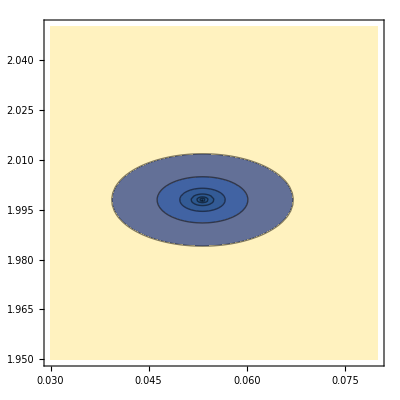

```mathematica
ContourPlot[Abs[PlotModeFunction[0,-2,2,1/100,4,ωr-ⅈ ωi,0,15]],{ωr,0.03,0.08},{ωi,1.95,2.05},Contours->{1/8,1/4,1/2,1,2,4,8}]
```

```mathematica
?PlotModeFunction
```

Arguments: n,s,m,a,Alm,ω,Nrcf,Nm
	 n -> Overtone level (integer).
	 s -> SpinWeight (integer).
	 m -> Azimuthal index (integer).
	 a -> Dimensionless spin parameter(rational or integer).
	 Alm -> Angular separation constant (integer).
	 Nrcf -> How deep into the continued fraction (integer).
	 Nm -> Number of azimuthal indecies(integer).

When in ContinuedFractionMode, package will require input for all the arguments and will use SelectMode
	 to replace ModeFunction with RadialCFRem.
When in PolynomialMode, n and Nrcf are not used in this plot function. Put dummy value in place.
PolynomialMode will use SelectMode to replace Modefunction with Starobinsky.

```mathematica
?ModeSolution
```

QNMSolution[n,s,l,m,a,ωg,Almg,ϵ,relax,Nrcf,Nm,ω0,Alm0,rl,rt] finds a solution of the coupled radial and angular Teukolsky equations with spin-weight s, 'magnetic' index m, and dimensionless angular momentum a.  ωg and Almg are initial guesses for the frequency and separation constant, which are assumed to be associated with azimuthal index l and overtone index n.

	The solution is found by iteration, calling AngularSpectralRoot and RadialLentzRoot until the magnitude of the change produced by either is less than 10^ϵ.  'relax' is an initial under-relaxation parameter used in updating the current guesses. For the radial equation, the continued fraction is truncated at the Nrcf^th term.  For the angular equation, Nm sets the size of the spectral approximation matrix.

	ω0, Alm0, rl, and rt are used to specify solution windows centered around the initial guesses ωg and Almg.  ω0 and Alm0 represent the prior solutions in a sequence of solutions.  |ω0-ωg| and |Alm0-Almg| set a length scale d for each solution.  The window for each solution is a portion of an anulus centered on the prior solution.  The difference between the inner and outer rings of the anulus is 2*rl*d with the guess solution centered between.  The width of the wedge is 2*rt*d along the outer ring.  Solutions falling outside the solution window for either quantity are rejected.  If rl=0 or rt=0, the solution is always accepted.

Options:
	 SolutionDebug→0 : Integer
		 Verbosity of debugging output for solutions iteration.  Increasing
		 value increases verbosity.
	 RadialDebug→0 : Integer
		 Verbosity of debugging output.  Increasing value increases verbosity.
	 RadialRelax→1: Rational(or Integer)
		 Under-relaxation parameter.
	 JacobianStep→-10
		 Log10 of relative step size used in numerical evaluation of the 
		 Jacobian in Newton's method.

```mathematica
?PlotModeFunction
```

Arguments: n,s,m,a,Alm,ω,Nrcf,Nm
	 n -> Overtone level (integer).
	 s -> SpinWeight (integer).
	 m -> Azimuthal index (integer).
	 a -> Dimensionless spin parameter(rational or integer).
	 Alm -> Angular separation constant (integer).
	 Nrcf -> How deep into the continued fraction (integer).
	 Nm -> Number of azimuthal indecies(integer).

When in ContinuedFractionMode, package will require input for all the arguments and will use SelectMode
	 to replace ModeFunction with RadialCFRem.
When in PolynomialMode, n and Nrcf are not used in this plot function. Put dummy value in place.
PolynomialMode will use SelectMode to replace Modefunction with Starobinsky.

```mathematica
SchwarzschildTTML[2,0,RadialDebug->1,SchDebug->0]
```

Computing (l=2,n=0)

δω=-0.000999500249999850200753259+0.000999999750249789883540794 ⅈ  root=0.814790684129320946548078

δω=-0.000293026998100418974970208+0.000292716642161629024499628 ⅈ  root=0.23860453352994433170791

δω=-4.288693947742206947529×10^-8-4.54463368441212505051966×10^-11 ⅈ  root=0.0000247028910080702197045188

KerrModes`Private`RadialLentzStep::pflag: Set $MinPrecision =32

δω=9.7452714890090918815619276061311×10^-19-4.5982187813861510023011623265972×10^-16 ⅈ  root=2.6485799663426761104701342344683×10^-13

KerrModes`Private`RadialLentzStep::pflag: Set $MinPrecision =48

δω=-2.24054451963581808753211165981620722065411131357×10^-34+5.28588024779398388053929234951524909564301604718×10^-32 ⅈ  root=3.04469437418045907328422309495722749033891767611×10^-29

SetPrecision::precsm: Requested precision 24 is smaller than $MinPrecision. Using $MinPrecision instead.

KerrModes`Private`RadialLentzStep::increase: Excessive increase in Precision, Abort

$Aborted

```mathematica
$MinPrecision=24
```

24

```mathematica
SelectMode[PolynomialMode]
```

Mode set to find Polynomial solutions

```mathematica
Plot3D[Abs[PlotModeFunctionL[0,-2,1,50/100,1,ωr-ⅈ ωi,300,15]],{ωr,0,1},{ωi,1,2}]
```

-Graphics3D-

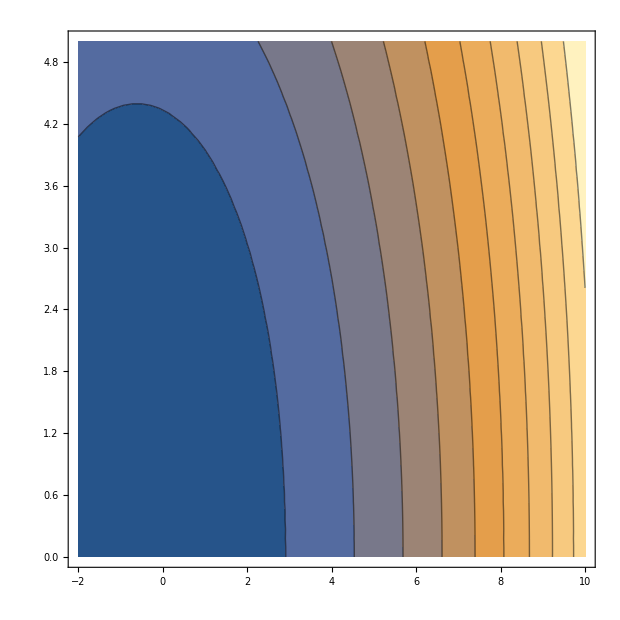

```mathematica
ContourPlot[Abs[PlotModeFunctionL[0,-2,-2,1/8,1,ωr-ⅈ ωi,3000,15]],{ωr,-2,10},{ωi,0,5},Contours->10]
```

```mathematica
Plot3D[{Re[PlotModeFunctionL[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]],Im[PlotModeFunctionL[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]]},{ωr,0,5},{ωi,0,5}]
```

-Graphics3D-

```mathematica
Plot3D[{Re[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]],Im[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]]},{ωr,0,4},{ωi,0,4}]
```

-Graphics3D-

```mathematica
RadialCFRem[0,-2,0,0,10,-ⅈ 10,2]
```

RadialCFRem[0,-2,0,0,10,-10 ⅈ,2]

```mathematica
SchwarzschildTTML[2,0,RadialDebug->1,SchDebug->0]
```

Computing (l=2,n=0)

Have made it into RadialCFRem

Have made it into RadialCFRem

Have made it into RadialCFRem

«17 more identical outputs»

KerrModes`Private`RadialLentzStep::increase: Excessive increase in Precision, Abort

$Aborted

```mathematica
?SchwarzschildTTML
```

SchwarzschildTTML[l,n] computes the Quasi-Normal Mode solutions for overtone n of mode l.  The mode is computed to an accuracy of 10^-14.  For given 'l', if solutions with overtones (n-1) and (n-2) have not been computed, then the routine is recersively called for overtone '(n-1).  If no solutions exist for mode l, then the first two overtones of (l-1) and (l-2) are used to extrapolate initial guesses for these modes.

Options:
	 SpinWeight→Null : -2,-1,0
		 The spin weight must be set via a call to SetSpinWeight before any KerrTTML
		 function call.
	 ModePrecision→24
	 JacobianStep→-10
		 The radial solver make use of numerical derivatives.  The relative step size
		 is set to 10^JacobianStep.
	 RadialCFMinDepth→300
		 The minimum value for the Radial Continued Fraction Depth.
	 RadialCFDepth→1
		 The initial Radial Continued Fraction Depth is usually taken from the prior 
		 solution in the sequence.  Fractional values reduce this initial value by that
		 fraction.  Integer values larger than RadialCFMinDepth are used as the new
		  initial value.
	 RadialRelax→1
		 Initial under-relaxation parameter used in Radial Newton iterations.
	 Rootϵ→-14
		 10^Rootϵ is the maximum allowed magnitude for the Radial Continued Fraction.
	 SchDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Schwarzschile iterations.
	 RadialDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial Newton iterations.